```mathematica
data=Import["/home/jure/Documents/opengl_ucenje/benchmarks/benchmarks.csv"];
data=Take[data,{11,data//Length}];
headers=Partition[data[[1]],11];
cols=data[[1]];
data=Take[data,{2,data//Length}];
```

```mathematica
benchmarks={"bitonic_2n_double_sort_bench", "bitonic_4n_double_sort_bench","bitonic_double_sort_bench", "std_double_sort_bench"};
cols
```

{bitonic_2n_float_sort_bench/8,884230,742.909,742.662,ns,,,,,,8}

```mathematica
GetBenchData[name_]:=Block [{tab},
tab=Table[If[(StringPosition[data[[i,1]], name]//Length  && Length[data[[i]]]>5)≠0,data[[i]], ""],{i,1,data//Length}];
tab=DeleteCases[tab, ""];
Return [tab];
];
```

```mathematica
data1=GetBenchData[benchmarks[[1]]];
data1=Take[data1, {1, (data1//Length)-2}];
timing1=data1[[All,4]];
NumToSort1=data1[[All,11]];
```

```mathematica
data2=GetBenchData[benchmarks[[2]]];
data2=Take[data2, {1, (data2//Length)-2}];
timing2=data2[[All,4]];
NumToSort2=data2[[All,11]];
```

```mathematica
data3=GetBenchData[benchmarks[[3]]];
data3=Take[data3, {1, (data3//Length)-2}];
timing3=data3[[All,4]];
NumToSort3=data3[[All,11]];
```

```mathematica
data4=GetBenchData[benchmarks[[4]]];
data4=Take[data4, {1, (data4//Length)-2}];
timing4=data4[[All,4]];
NumToSort4=data4[[All,11]];
```

```mathematica
p1=Transpose[{NumToSort1,timing1}];
p2=Transpose[{NumToSort2,timing2}];
p3=SortBy[Transpose[{NumToSort3,timing3}], First]
p4=SortBy[Transpose[{NumToSort4,timing4}], First];
```

{{10,1030.15},{20,1196.92},{40,1577.49},{50,2111.4},{80,2564.73},{100,2916.67},{200,5492.63},{400,11994.4},{800,25343.6},{1600,57162.4},{3200,128596},{5000,223778},{7500,333358},{10000,504446},{12000,608750},{15000,767722},{17000,960893},{20000,1.13258×10^6},{25000,1.43501×10^6},{27000,1.51865×10^6},{30000,1.7149×10^6},{35000,2.21873×10^6},{40000,2.5509×10^6},{50000,3.15566×10^6},{70000,5.28413×10^6},{100000,7.30362×10^6},{120000,8.95528×10^6},{150000,1.24854×10^7},{200000,1.74228×10^7},{400000,3.86372×10^7},{600000,6.56545×10^7},{800000,8.75848×10^7},{1.×10^6,1.12179×10^8},{1.2×10^6,1.49374×10^8},{1.5×10^6,1.86284×10^8},{1.8×10^6,2.18918×10^8},{2.×10^6,2.52241×10^8},{2.5×10^6,3.22998×10^8},{3.×10^6,4.05359×10^8},{5.×10^6,7.82101×10^8},{7.×10^6,1.08856×10^9},{1.×10^7,1.69211×10^9}}

```mathematica
color=ColorData[10,"ColorList"];
LegendFontSize=20;
legenda=
PointLegend[{
{color[[1]],AbsolutePointSize[8]},
{color[[2]],AbsolutePointSize[8]},
{color[[3]],AbsolutePointSize[8]},
{color[[4]], AbsolutePointSize[8]},
Directive[color[[9]], AbsolutePointSize[8]]},
{Style["bitonic 2^n sort", LegendFontSize], Style["bitonic 8n sort", LegendFontSize], Style["bitonic arbitrary sort", LegendFontSize], 
Style["std sort", LegendFontSize]},
LegendLabel->"", LegendLayout->{"Row",6}];
```

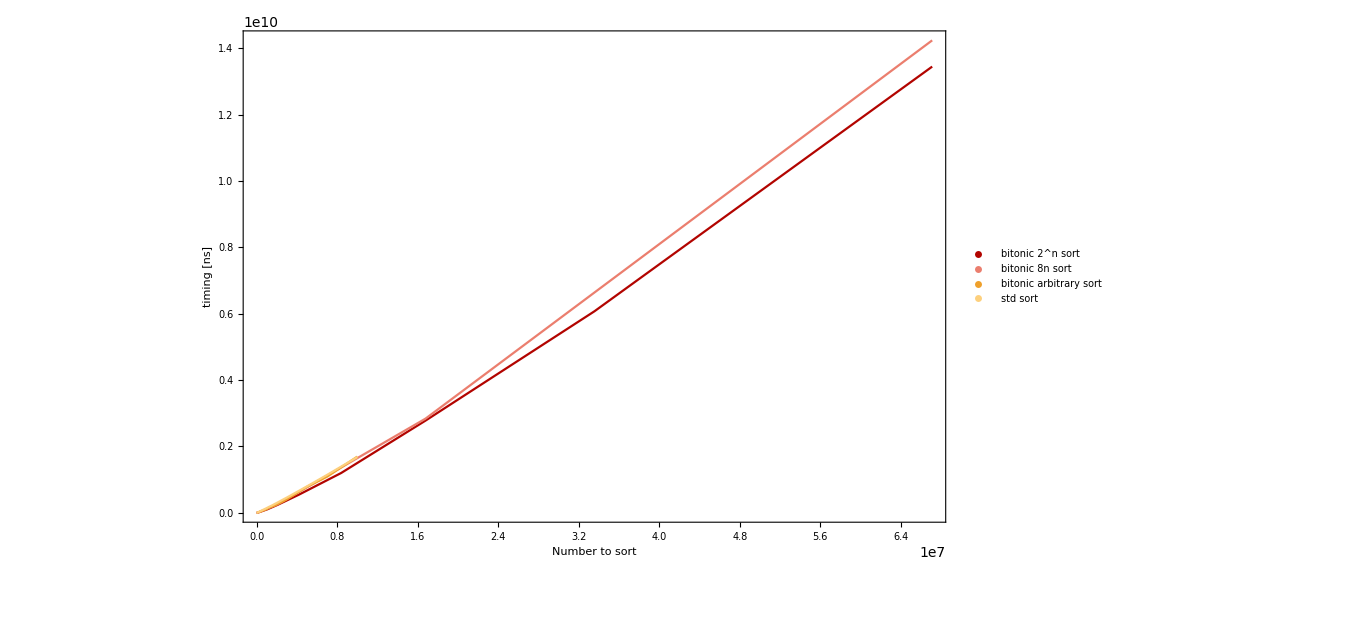

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {1*10^7, 7*10^9}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->All,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

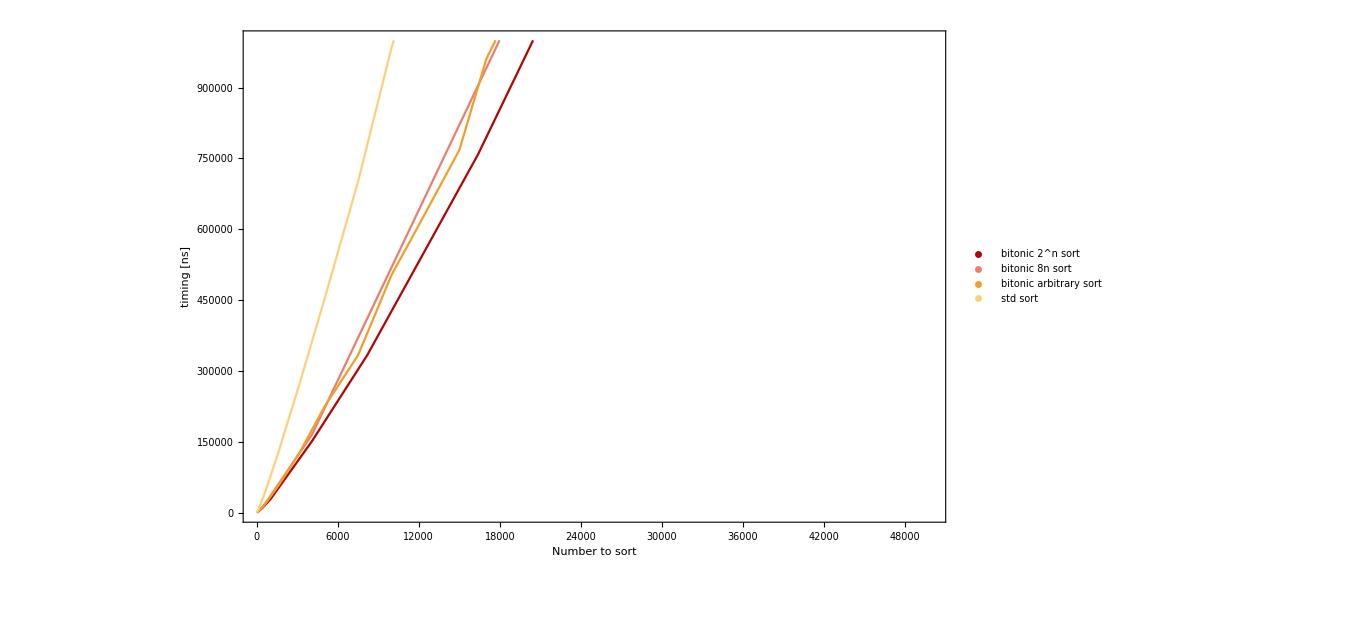

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
p1,p2,p3,p4
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]], color[[6]]},
Epilog->Inset[legenda, {4*10^4, 2.2*10^5}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0, 50000},{0, 10 ^6}},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

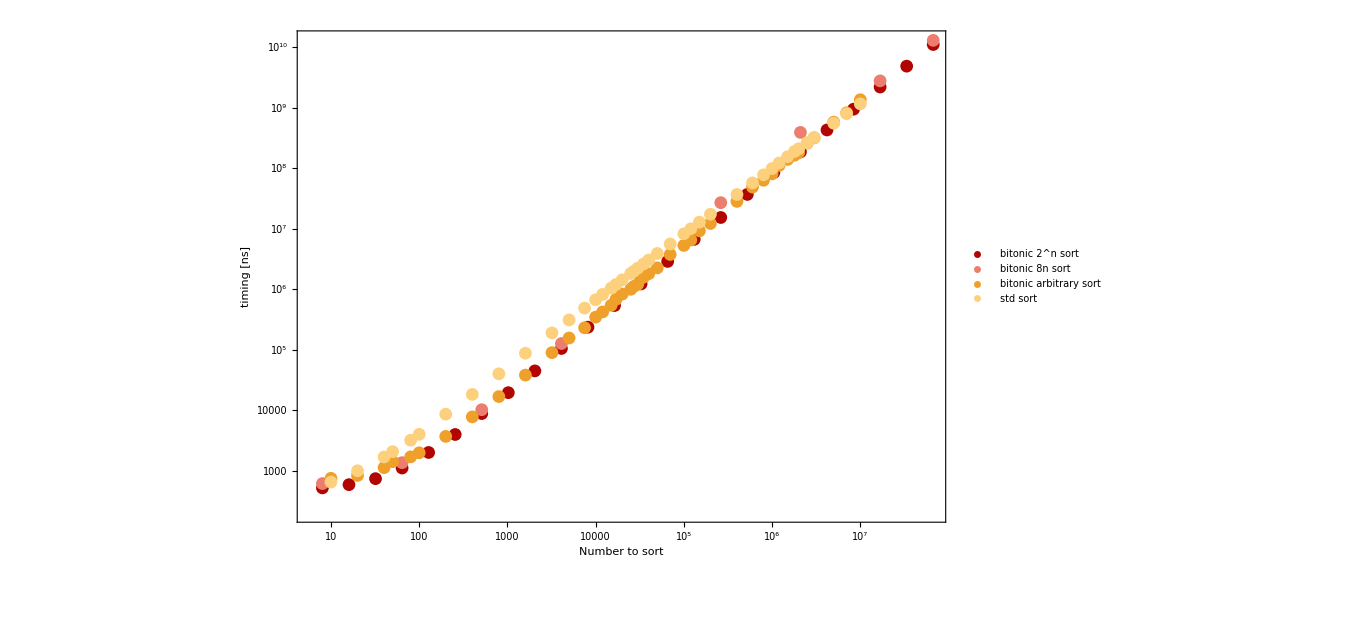

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLogLogPlot[{
p1,p2,p3, p4
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["timing [ns]", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]], color[[5]]},
Epilog->Inset[legenda, {1*10^6, 2*10^8}],
AxesOrigin->{-100, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->Automatic,
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

```mathematica
NonlinearModelFit[Take[p1, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p2, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p3, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
NonlinearModelFit[Take[p4, -5],a*x^2+b*x*Log[x]^2+ c*x,{a,b,c},x]
```

FittedModel[-23.9515 x+2.00726×10^-7 x^2+0.544064 x Log[x]^2]

FittedModel[287.983 x+1.04055×10^-6 x^2-0.50207 x Log[x]^2]

FittedModel[227.51 x+7.53376×10^-6 x^2-0.642778 x Log[x]^2]

FittedModel[37.8328 x-4.32959×10^-7 x^2+0.31953 x Log[x]^2]

```mathematica
(*speedup calculation in comparison to std*)

speedup1=Table[{p3[[i,1]],p4[[i,2]]/p3[[i,2]]},{i,1,p3//Length}]//N;
```

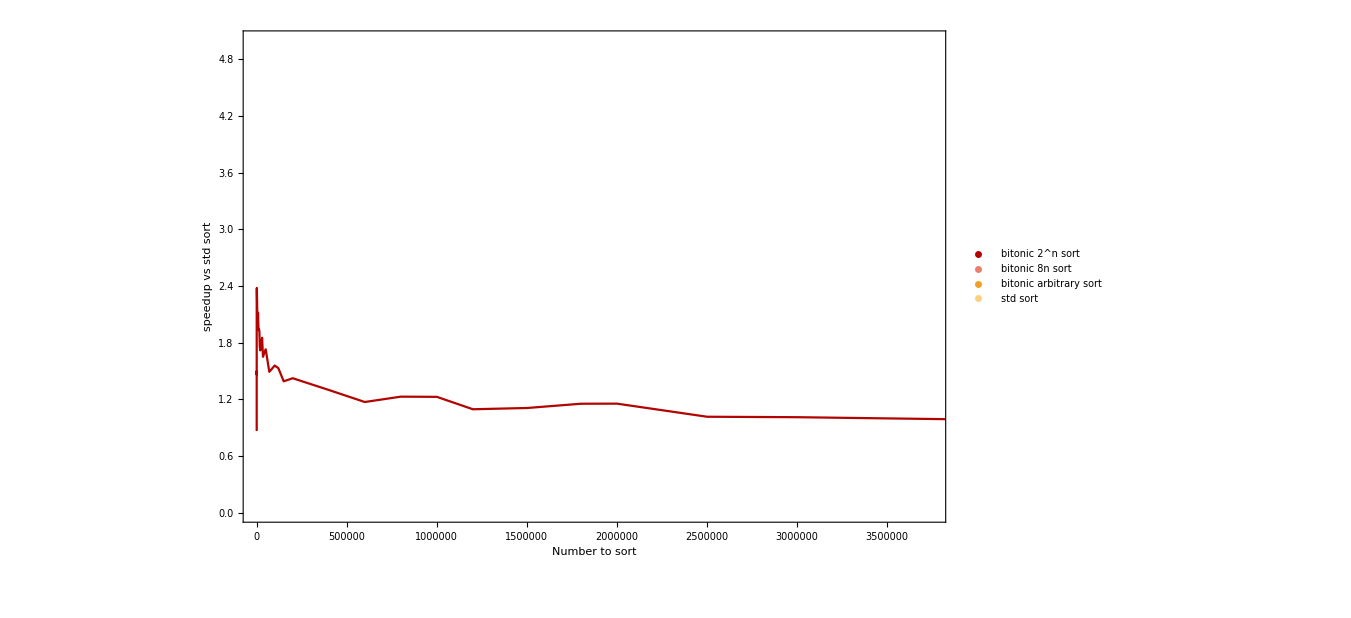

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{Automatic,{0,5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```

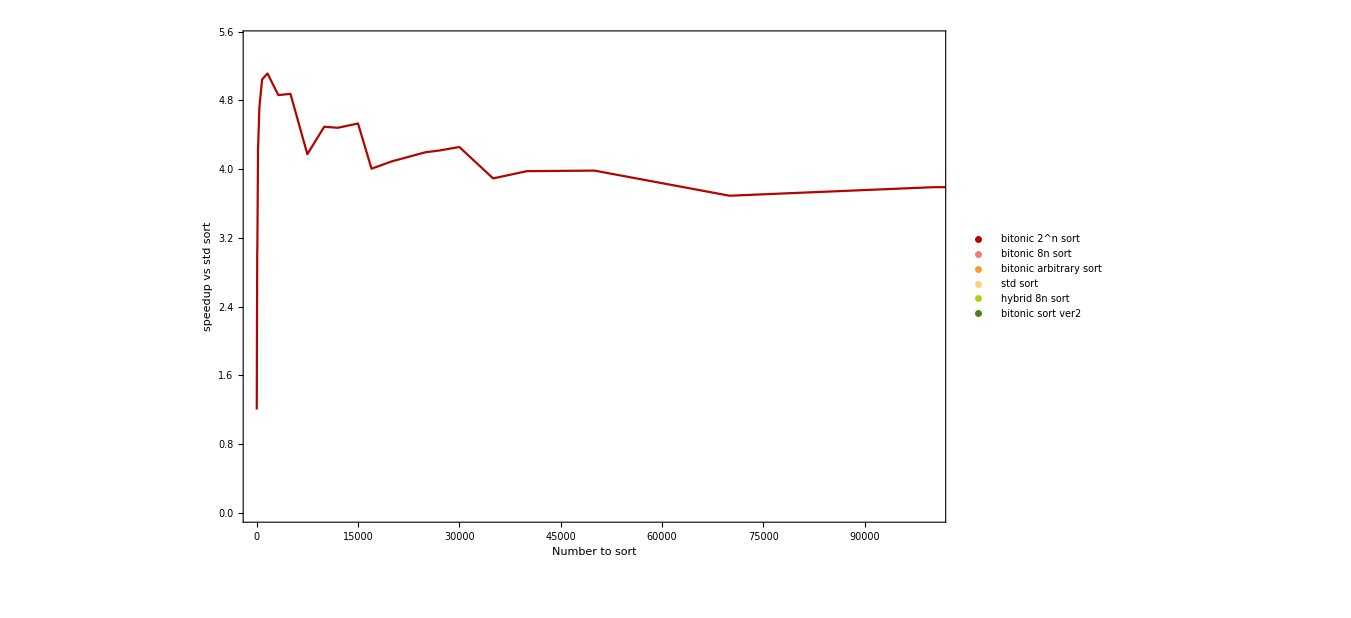

```mathematica
leftP=Automatic;
rightP=20;
topP=Automatic;
bottomP=Automatic;
ListLinePlot[{
speedup1
}, Frame->True, ImageSize->1000, FrameLabel->{Style["Number to sort", 20], Style["speedup vs std sort", 20]},
PlotStyle->{color[[1]],color[[2]], color[[3]], color[[4]]},
Epilog->Inset[legenda, {2*10^6, 8*10^8}],
AxesOrigin->{-10, -10},
Frame->True, 
FrameTicks->True,
FrameTicksStyle->Directive[Black,FontSize->18],
ImageSize->700,
PlotRange->{{0,100000},{0,5.5}},
FrameLabel->{Style["Δa_0",FontSize-> 24], Style["w",Italic,FontSize-> 24]},
ImagePadding->{{leftP, rightP},{bottomP, topP}}]
```